```mathematica
Quit
```

# Function

## Definition and Plot

```mathematica
f[x_]:=x^(2);
```

```mathematica
f[2]
```

4

```mathematica
f[16]
```

256

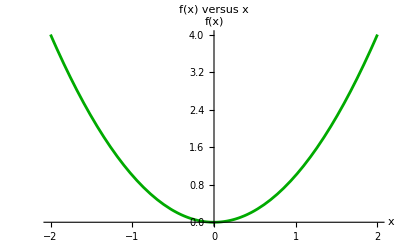

```mathematica
P1=Plot[f[x],{x,-2,2},AxesLabel->{"x","f(x)"},PlotStyle->Darker[Green],PlotLabel->"f(x) versus x"]
```

```mathematica
g[x_]:=x+1;
```

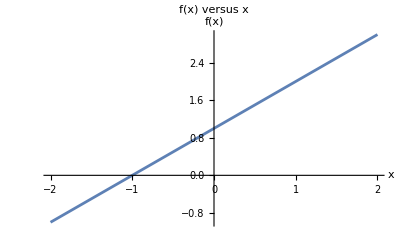

```mathematica
P2=Plot[g[x],{x,-2,2},AxesLabel->{"x","f(x)"},PlotLabel->"f(x) versus x"]
```

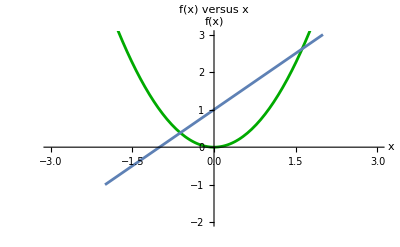

```mathematica
Show[P1,P2,PlotRange->{{-3,3},{-2,3}}]
```